# Thesis Project: Cement Hydrates C-H-S

## K-Points Analysis DFTB+

### Working directory and Figures directory

```mathematica
wrkdir = "/home/qbit/Documents/git-repositories/bachelor-thesis/";
SetDirectory[wrkdir];
```

```mathematica
figDir="/home/qbit/Documents/git-repositories/bachelor-thesis/figures/"
```

/home/qbit/Documents/git-repositories/bachelor-thesis/figures/

### The k-point grid

```mathematica
bulk = Import["./dftb/eos/POSCAR-init", "Table"];
```

```mathematica
lattbulk = bulk[[2, 1]] bulk[[3;;5]]
```

{{13.5354,0.18446,0.00755401},{-16.2629,24.8887,-0.00875423},{0.543338,-0.483321,23.4374}}

```mathematica
{a, b, c} = lattbulk;
```

```mathematica
Δk = Table[0.07-0.005 i, {i, 0, 10}];
```

```mathematica
Δk//Map[{#, Round[((b×c)/((a×b).c)//Norm)/#],
Round[((c×a)/((a×b).c)//Norm)/#],
Round[((a×b)/((a×b).c)//Norm)/#]}&, #]&//TableForm
```

0.07 | 1 | 1 | 1
0.065 | 1 | 1 | 1
0.06 | 1 | 1 | 1
0.055 | 2 | 1 | 1
0.05 | 2 | 1 | 1
0.045 | 2 | 1 | 1
0.04 | 2 | 1 | 1
0.035 | 2 | 1 | 1
0.03 | 3 | 1 | 1
0.025 | 3 | 2 | 2
0.02 | 4 | 2 | 2

We will run the xkp.sh script for k-points densities 0.06, 0.04, and 0.03

### Convergency of k-points

```mathematica
data = Import["./dftb/kp.dat"]
```

{{1,-4660.48,43},{2,-4660.51,58},{3,-4660.51,37}}

```mathematica
kpdat =data[[All,{1,2}]]//Map[#/{1,690}&]
```

{{1,-6.75432},{2,-6.75437},{3,-6.75436}}

#### Get the x and y data:

```mathematica
kpY=kpdat[[All,2]]
kpX={0.06,0.04,0.03}
```

{-6.75432,-6.75437,-6.75436}

{0.06,0.04,0.03}

#### Plot the data:

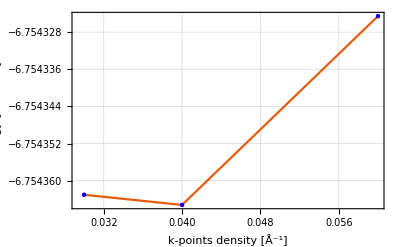

```mathematica
kpPlotNoWindow=ListPlot[
Transpose[{kpX,kpY}],
PlotTheme->"Scientific",
GridLines->Automatic,
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Blue]},
Frame->True,
FrameLabel->
{"k-points density [Å^-1]", "Energy [eV/atom]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400]
```

```mathematica
Export[FileNameJoin[{figDir,"kp-dftb-nw.png"}], kpPlotNoWindow, ImageResolution->300];
```

#### Let’s analyse the convergency of these data using the 1 meV/atom criteria

```mathematica
energyMin=kpdat[[1,2]]+10^-3/2;
energyMax=kpdat[[1,2]]-10^-3/2;
```

```mathematica
kPlot=ListPlot[
Transpose[{kpX,kpY}],
PlotRange->{kpdat[[1,2]]+10^-3, kpdat[[1,2]]-10^-3},
PlotTheme->"Scientific",
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Blue]},
Frame->True,
FrameLabel->
{"k-points density [Å^-1]", "Energy [eV/atom]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400];
```

```mathematica
energyWindow=Graphics[{(*Shaded rectangle*){Gray,Opacity[0.3],Rectangle[{0.02,energyMin},{0.07,energyMax}]},(*Dashed lines for rectangle edges*){Dashed,Black,Line[{{0.02,energyMin},{0.07,energyMin}}]},{Dashed,Black,Line[{{0.02,energyMax},{0.07,energyMax}}]},(*Double-headed arrow with annotation*){Arrowheads[{-0.02,0.02}],Arrow[{{0.05,energyMin},{0.05,energyMax}}]},Text[Style["1 meV",FontSize->12,Black],{0.053,0.0001+Mean[{energyMin,energyMax}]}]}];
```

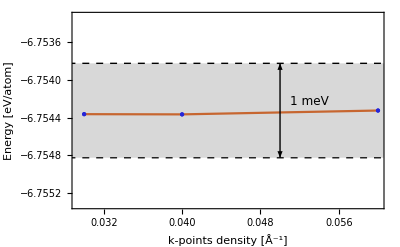

```mathematica
kpPlotWindow =Show[kPlot, energyWindow]
```

```mathematica
Export[FileNameJoin[{figDir,"kp-dftb-w.png"}], kpPlotWindow, ImageResolution->300];
```

From this result, we use from now on the k-point grid 1x1x1

## Cut-off Energy Analysis VASP

### ENCUT

```mathematica
datacem = Import["./dftb/ecut.dat"];
```

```mathematica
dataecut=datacem[[All,{1,2}]]//Map[#/{1,690}&];
```

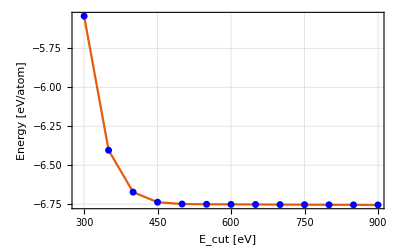

```mathematica
encutPlotNoWindow= dataecut//ListPlot[#,
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
FrameLabel->{"E_cut [eV]","Energy [eV/atom]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Blue, AbsolutePointSize[5],
Point[#]}
]&
```

```mathematica
Export[FileNameJoin[{figDir,"encut-nw.png"}], encutPlotNoWindow, ImageResolution->300];
```

We  use meV precision because magnetic properties are really tiny. So we need this precision to describe these properties.

```mathematica
encutMin=dataecut[[13,2]];
encutMax=dataecut[[13,2]]+10^-3;
```

```mathematica
encutPlot =dataecut//ListPlot[#,
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
FrameLabel->{"E_cut [eV]","Energy [meV/atom]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->All,(*{{350,950},{dataecut[[13,2]], dataecut[[2,2]]}},*)
InterpolationOrder->1,
ImageSize->400,
Epilog->{Blue, AbsolutePointSize[5],
Point[#]}
]&;
```

```mathematica
encutWindow=Graphics[{(*Shaded rectangle*){Gray,Opacity[0.3],Rectangle[{200,encutMin},{950,encutMax}]},(*Dashed lines for rectangle edges*){Dashed,Black,Line[{{200,encutMin},{950,encutMin}}]},{Dashed,Black,Line[{{200,encutMax},{950,encutMax}}]},(*Double-headed arrow with annotation*){Arrowheads[{-0.02,0.02}],Arrow[{{750,encutMin},{750,encutMax}}]},Text[Style["1 meV",FontSize->12,Black],{800,Mean[{encutMin,encutMax}]}]}];
```

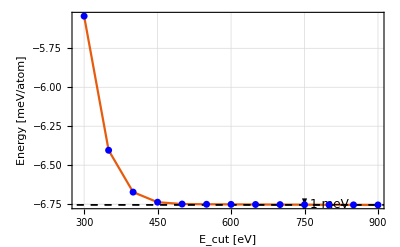

```mathematica
encutPlotWindow=Show[encutPlot,encutWindow]
```

We  use 800 meV for  CSH analysis from now on.

```mathematica
Export[FileNameJoin[{figDir,"encut-w.png"}], encutPlotWindow, ImageResolution->300];
```

## K-Points Analysis VASP

```mathematica
kpDataVasp=Import["./cluster-files/kp.dat"][[All, {1,2}]]//Map[#/{1,690}&]
```

{{1,-6.75432},{2,-6.75437},{3,-6.75436}}

```mathematica
kpDataVasp[[All, 2]]
```

{-6.75432,-6.75437,-6.75436}

```mathematica
kPlotVaspNw = ListPlot[
Transpose[{kpX,kpDataVasp[[All, 2]]}],
PlotTheme->"Scientific",
GridLines->Automatic,
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Blue]},
Frame->True,
FrameLabel->
{"k-points density [Å^-1]", "Energy [eV/atom]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400]
```

-Graphics-

```mathematica
Export[FileNameJoin[{figDir,"kp-vasp-nw.png"}], kPlotVaspNw, ImageResolution->300];
```

```mathematica
energyMinVasp=kpDataVasp[[1,2]]+10^-3/2;
energyMaxVasp=kpDataVasp[[1,2]]-10^-3/2;
```

```mathematica
kPlotVasp=ListPlot[
Transpose[{kpX,kpDataVasp[[All, 2]]}],
PlotRange->{kpDataVasp[[1,2]]+10^-3, kpDataVasp[[1,2]]-10^-3},
PlotTheme->"Scientific",
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Blue]},
Frame->True,
FrameLabel->
{"k-points density [Å^-1]", "Energy [eV/atom]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400];
```

```mathematica
energyWindowVasp=Graphics[{(*Shaded rectangle*){Gray,Opacity[0.3],Rectangle[{0.02,energyMinVasp},{0.07,energyMaxVasp}]},(*Dashed lines for rectangle edges*){Dashed,Black,Line[{{0.02,energyMinVasp},{0.07,energyMinVasp}}]},{Dashed,Black,Line[{{0.02,energyMaxVasp},{0.07,energyMaxVasp}}]},(*Double-headed arrow with annotation*){Arrowheads[{-0.02,0.02}],Arrow[{{0.05,energyMinVasp},{0.05,energyMaxVasp}}]},Text[Style["1 meV",FontSize->12,Black],{0.053,0.0001+Mean[{energyMinVasp,energyMaxVasp}]}]}];
```

```mathematica
kPlotVaspW=Show[kPlotVasp, energyWindowVasp]
```

-Graphics-

```mathematica
Export[FileNameJoin[{figDir,"kp-vasp-w.png"}], kPlotVaspW, ImageResolution->300];
```

## Density of States

```mathematica
pdosData=Import["./cluster-files/DOSCAR-cem1.sto", "Table"];
```

```mathematica
Dimensions[pdosData]
```

{2074387}

```mathematica
dos = pdosData[[7;;7+3000]][[All, {1, 2}]];
```

```mathematica
ef = pdosData[[6, 4]]
```

3.069

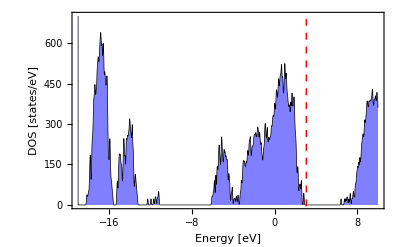

```mathematica
ListPlot[dos, 
PlotTheme->"Scientific",
Joined->True,
Axes->False,
Frame->True,
FrameLabel->
{"Energy [eV]", 
"DOS [states/eV]"},
GridLines->{{ef}, None},
GridLinesStyle-> 
Directive[Red, Dashed,
AbsoluteThickness[1]],
BaseStyle->
{FontFamily->"Helvetica",
FontSize->15},
Filling->Axis,
FillingStyle->
Directive[Opacity[0.5], Blue],
PlotStyle-> 
{AbsoluteThickness[0.5], Black},
ImageSize->400,
PlotRange->{All, {0, 700}}]
```

### Partial Density of States PDOS

Let us define the number of atoms of each element.

```mathematica
atomsCa=99;
atomsSi=60;
atomsO=323;
atomsH=208;
```

## Benchmark

```mathematica
benchRes=Import["./cluster-files/results.dat"]
```

{{1,552.512},{2,308.492},{3,235.218},{5,186.864},{7,213.865},{9,187.9},{11,228.094}}

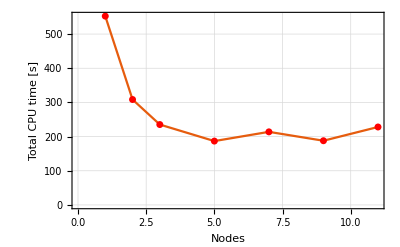

```mathematica
ListPlot[benchRes,
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
FrameLabel->{"Nodes","Total CPU time [s]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->True,InterpolationOrder->1,ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[benchRes]}]
```

```mathematica
benchRes[[All,1]];
```

```mathematica
scaleTCPU=benchRes//Map[#/{1,benchRes[[1,2]]}&];
```

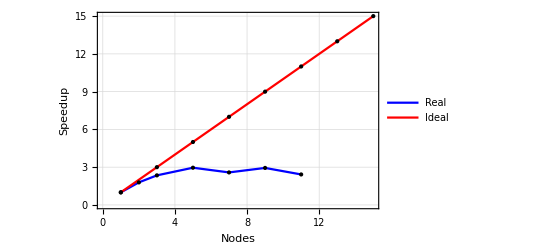

```mathematica
ListPlot[{
Transpose[{scaleTCPU[[All,1]],1/scaleTCPU[[All,2]]}],
Transpose[{Range[1,15,2], Range[1,15,2]}]},
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
FrameLabel->{"Nodes","Speedup"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->True,InterpolationOrder->1,ImageSize->400,
PlotStyle->{Blue, Red},
PlotLegends->Placed[{"Real", "Ideal"} ,After],
Mesh->All,
MeshStyle->
{Directive[PointSize[Medium], Black]}]
```

## MLFF Results Analysis (Training)

```mathematica
wrkdir = "/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files/";
SetDirectory[wrkdir]
```

/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files

### Optimal Volume

```mathematica
optVolumeTraining=Import["volume-t.dat"][[All,1]];
```

```mathematica
timeData=2/10^3 Range[0,50000-1]; (*In μs*)
```

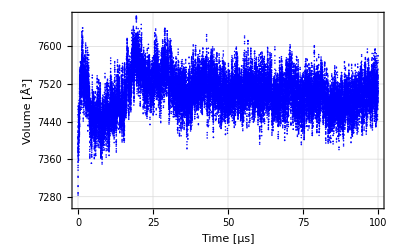

```mathematica
optVolPlotT=ListPlot[
Transpose[{timeData,optVolumeTraining}],
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
FrameLabel->{"Time [μs]","Volume [Å^3]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->False,
PlotRange->All,PlotStyle->Blue,
ImageSize->400]
```

```mathematica
Export[FileNameJoin[{figDir,"opt-vol-t.png"}], optVolPlotT, ImageResolution->300];
```

### Total Energy

```mathematica
totEnergyT=Import["entot.dat"][[All,1]];
```

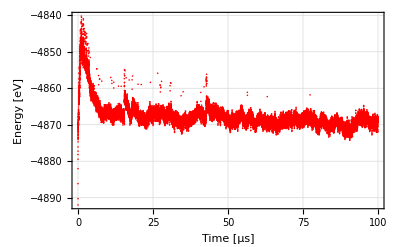

```mathematica
totEnergyPlotT=ListPlot[
Transpose[{timeData,totEnergyT}],
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
FrameLabel->{"Time [μs]","Energy [eV]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->False,
PlotRange->All,PlotStyle->Red,
ImageSize->400]
```

```mathematica
Export[FileNameJoin[{figDir,"toten-t.png"}],totEnergyPlotT, ImageResolution->300];
```

### BEEF & ERR

Get the beef and err data from the ML_LOGFILE from the training process

```mathematica
Run["grep 'BEEF' ML_LOGFILE-t | tail -n +15 | awk '{print $2\"   \"$4}' > beef-t.dat"];
```

```mathematica
beefData = Import["beef-t.dat"];
```

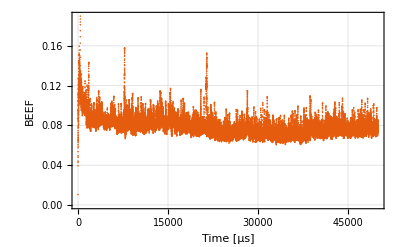

```mathematica
beefPlotT=beefData//ListPlot[#,PlotRange->All,
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
Joined->False,
FrameLabel->{"Time [μs]","BEEF"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400]&
```

```mathematica
Export[FileNameJoin[{figDir,"beef-t.png"}], beefPlotT, ImageResolution->300];
```

## MLFF Results Analysis (Prediction)

### Optimal Volume

```mathematica
optVolumePredict=Import["volume-p.dat"][[All,1]];
```

```mathematica
timeDataPredict=2/10^3 Range[0,47858-1]; (*In μs*)
```

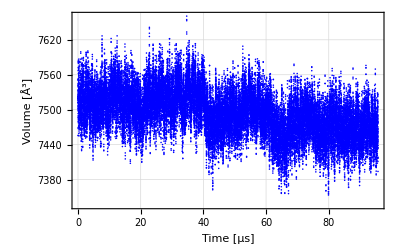

```mathematica
optVolPlotP=ListPlot[
Transpose[{timeDataPredict,optVolumePredict}],
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
FrameLabel->{"Time [μs]","Volume [Å^3]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->False,
PlotRange->All,PlotStyle->Blue,
ImageSize->400]
```

```mathematica
Export[FileNameJoin[{figDir,"opt-vol-p.png"}], optVolPlotP, ImageResolution->300];
```

### Total Energy

```mathematica
totEnergyP=Import["entot-p.dat"][[All,1]];
```

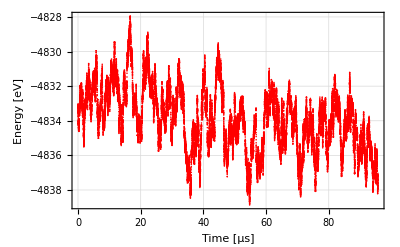

```mathematica
totEnergyPlotP=ListPlot[
Transpose[{timeDataPredict,totEnergyP}],
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
FrameLabel->{"Time [μs]","Energy [eV]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->False,
PlotRange->All,PlotStyle->Red,
ImageSize->400]
```

```mathematica
Export[FileNameJoin[{figDir,"toten-p.png"}],totEnergyPlotP, ImageResolution->300];
```

### BEEF & ERR

Get the beef and err data from the ML_LOGFILE from the training process

```mathematica
Run["grep 'BEEF' ML_LOGFILE-p | tail -n +15 | awk '{print $2\"   \"$4}' > beef-p.dat"];
```

```mathematica
beefData = Import["beef-p.dat"];
```

```mathematica
beefData//ListPlot[#,PlotRange->All,
PlotTheme->"Scientific",
GridLines->Automatic,
Frame->True,
Joined->False,
FrameLabel->{"Time [μs]","BEEF"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400]&
```

-Graphics-

## Optimal Hyperparameters

### RCUT 1

```mathematica
rcut1Error=Import["ml_error/rcut1/training_error.dat"];
```

```mathematica
(*Extract numerical data*)
rcut1Data=rcut1Error[[2;;38]]
```

{{4.,0.0032836,0.176228,0.835922},{5.,0.00325208,0.174789,0.811028},{6.,0.00336596,0.172381,0.788002},{7.,0.00349476,0.170336,0.793092},{8.,0.00364567,0.168727,0.785038},{9.,0.00359502,0.166877,0.792586},{10.,0.00340678,0.164885,0.801779},{11.,0.00323127,0.162856,0.804916},{12.,0.00301756,0.160337,0.81601},{13.,0.00273146,0.157803,0.812309},{14.,0.00256878,0.15479,0.810131},{15.,0.00234377,0.151665,0.793498},{16.,0.0022141,0.148477,0.761627},{17.,0.00193729,0.145187,0.756035},{18.,0.0018221,0.141737,0.77235},{19.,0.001776,0.13873,0.761984},{20.,0.00163404,0.136197,0.792159},{21.,0.00157933,0.133959,0.815209},{22.,0.00148081,0.131881,0.811386},{23.,0.0012774,0.129917,0.811758},{24.,0.0011298,0.127832,0.816307},{25.,0.0010516,0.126057,0.822936},{26.,0.000974993,0.124453,0.860402},{27.,0.000997187,0.122922,0.869522},{28.,0.00102583,0.121511,0.85787},{29.,0.000998005,0.120299,0.854101},{30.,0.000942154,0.119191,0.850257},{31.,0.0008914,0.118174,0.836578},{32.,0.000874307,0.117382,0.820385},{33.,0.000856561,0.11664,0.807333},{34.,0.000826352,0.115794,0.797799},{35.,0.000820932,0.115005,0.788736},{36.,0.000814705,0.11444,0.786377},{37.,0.000817444,0.113975,0.791028},{38.,0.00083405,0.113438,0.793737},{39.,0.000851354,0.112868,0.789816},{41.,0.000857697,0.111982,0.795895}}

```mathematica
(*Extract rcut values and each column*)
rcutValues1=rcut1Data[[All,1]];
energyValues1=rcut1Data[[All,2]];
forceValues1=rcut1Data[[All,3]];
stressValues1=rcut1Data[[All,4]];
```

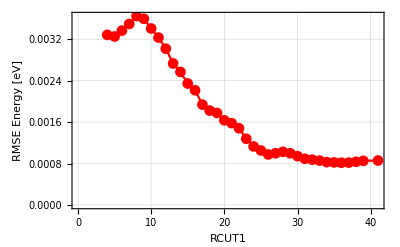

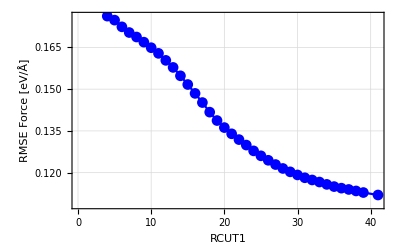

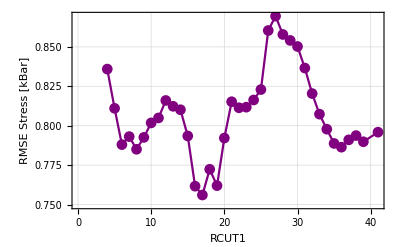

```mathematica
energyPlot1=
ListLinePlot[
Transpose[{rcutValues1,energyValues1}],
PlotMarkers->Automatic,
PlotStyle->Red,
Frame->True,
FrameLabel->{"RCUT1","RMSE Energy [eV]"},
GridLines->Automatic,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific" 
];

forcePlot1=
ListLinePlot[Transpose[{rcutValues1,forceValues1}],
PlotMarkers->Automatic,
PlotStyle->Blue,
Frame->True,
FrameLabel->{"RCUT1","RMSE Force [eV/Å]"},
GridLines->Automatic,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific"
];

stressPlot1=
ListLinePlot[Transpose[{rcutValues1,stressValues1}],
PlotMarkers->Automatic,
PlotStyle->Purple,
Frame->True,
FrameLabel->{"RCUT1","RMSE Stress [kBar]"},
GridLines->Automatic,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific"
];

(*Show all plots separately*)
energyPlot1
forcePlot1
stressPlot1
```

```mathematica
Export[FileNameJoin[{figDir,"rcut-1-energy.png"}], energyPlot1, ImageResolution->300];
Export[FileNameJoin[{figDir,"rcut-1-force.png"}], forcePlot1, ImageResolution->300];
Export[FileNameJoin[{figDir,"rcut-1-stress.png"}], stressPlot1, ImageResolution->300];
```

### RCUT 2

```mathematica
rcut2Error=Import["ml_error/rcut2/training_error.dat"];
```

```mathematica
(*Extract numerical data*)
rcut2Data=rcut2Error[[2;;]];
```

```mathematica
(*Extract rcut values and each column*)
rcutValues2=rcut2Data[[All,1]];
energyValues2=rcut2Data[[All,2]];
forceValues2=rcut2Data[[All,3]];
stressValues2=rcut2Data[[All,4]];
```

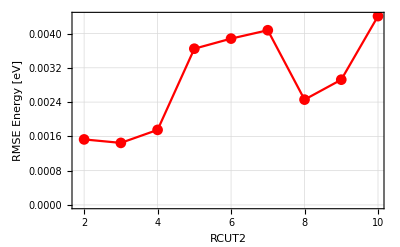

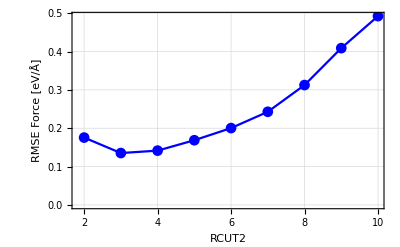

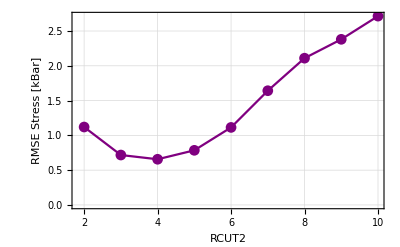

```mathematica
energyPlot2=
ListLinePlot[
Transpose[{rcutValues2,energyValues2}],
PlotMarkers->Automatic,
PlotStyle->Red,
Frame->True,
FrameLabel->{"RCUT2","RMSE Energy [eV]"},
GridLines->Automatic,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific" 
];

forcePlot2=
ListLinePlot[Transpose[{rcutValues2,forceValues2}],
PlotMarkers->Automatic,
PlotStyle->Blue,
Frame->True,
FrameLabel->{"RCUT2","RMSE Force [eV/Å]"},
GridLines->Automatic,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific" 
];

stressPlot2=
ListLinePlot[Transpose[{rcutValues2,stressValues2}],
PlotMarkers->Automatic,
PlotStyle->Purple,
Frame->True,
FrameLabel->{"RCUT2","RMSE Stress [kBar]"},
GridLines->Automatic,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific" 
];

(*Show all plots separately*)
energyPlot2
forcePlot2
stressPlot2
```

```mathematica
Export[FileNameJoin[{figDir,"rcut-2-energy.png"}], energyPlot2, ImageResolution->300];
Export[FileNameJoin[{figDir,"rcut-2-force.png"}], forcePlot2, ImageResolution->300];
Export[FileNameJoin[{figDir,"rcut-2-stress.png"}], stressPlot2, ImageResolution->300];
```

## RMSE ENERGY, FORCE & STRESS

### TOTAL ENERGY

```mathematica
dtfTOTEN=Import["ml_error/dft_data/dft_toten.dat"];
```

```mathematica
mlTOTEN=Import["ml_error/ml_data/ml_toten.dat"];
```

```mathematica
rmseTOTEN= (mlTOTEN[[All,2]] - dtfTOTEN[[All,2]])/690;
```

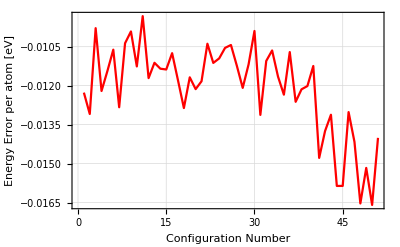

```mathematica
rmseTotenPlot=ListLinePlot[rmseTOTEN,
PlotRange->All,
PlotTheme->"Scientific" ,
GridLines->Automatic,
PlotStyle->Red,Frame->True,
Joined->True,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
FrameLabel->{"Configuration Number","Energy Error per atom [eV]"}]
```

```mathematica
Export[FileNameJoin[{figDir,"rmse-toten-plot.png"}], rmseTotenPlot, ImageResolution->300];
```

### RMSE FORCE

```mathematica
rmseForce=Import["ml_error/ml_rmse_force.dat"];
```

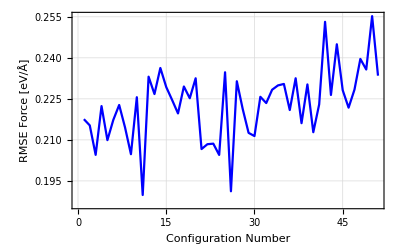

```mathematica
rmseForcePlot=ListLinePlot[rmseForce[[2;;]],
PlotRange->All,
PlotTheme->"Scientific" ,
GridLines->Automatic,
PlotStyle->Blue,Frame->True,
Joined->True,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
FrameLabel->{"Configuration Number","RMSE Force [eV/Å]"}]
```

```mathematica
Export[FileNameJoin[{figDir,"rmse-force-plot.png"}], rmseForcePlot, ImageResolution->300];
```

### RMSE STRESS

```mathematica
rmseStress=Import["ml_error/rmse_stress.dat"][[2;;,All]];
```

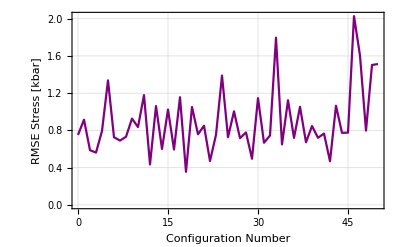

```mathematica
rmseStressPlot=ListLinePlot[rmseStress,
PlotRange->All,
PlotTheme->"Scientific" ,
GridLines->Automatic,
PlotStyle->Purple,Frame->True,
Joined->True,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
FrameLabel->{"Configuration Number","RMSE Stress [kbar]"}]
```

```mathematica
Export[FileNameJoin[{figDir,"rmse-stress-plot.png"}], rmseStressPlot, ImageResolution->300];
```